```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_Tscaling_mub0/buffer/mSigma.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub0/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub50/buffer/mSigma.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub50/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub50=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub50=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub50[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub50linear=Transpose[{T0[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub50[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub100/buffer/mSigma.dat"]];
T100=Flatten[Import["./LPA_Tscaling_mub100/buffer/TMeV.dat"]];
t=-(T100-T100[[1]])/T100[[1]];
datamub100=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub100=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T100]-2}]]}];
b1mub100linear=Transpose[{T100[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub100[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T100]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub150/buffer/mSigma.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub150/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub150=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub150=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub150[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub150linear=Transpose[{T0[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub150[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub200/buffer/mSigma.dat"]];
T200=Flatten[Import["./LPA_Tscaling_mub200/buffer/TMeV.dat"]];
t=-(T200-T200[[1]])/T200[[1]];
datamub200=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub200=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T200]-2}]]}];
b1mub200linear=Transpose[{T200[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub200[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T200]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub250/buffer/mSigma.dat"]];
T250=Flatten[Import["./LPA_Tscaling_mub250/buffer/TMeV.dat"]];
t=-(T250-T250[[1]])/T250[[1]];
datamub250=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub250=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub250[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T250]-2}]]}];
b1mub250linear=Transpose[{T250[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub250[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T250]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub300/buffer/mSigma.dat"]];
T300=Flatten[Import["./LPA_Tscaling_mub300/buffer/TMeV.dat"]];
t=-(T300-T300[[1]])/T300[[1]];
datamub300=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
b1mub300linear=Transpose[{T300[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub350/buffer/mSigma.dat"]];
T350=Flatten[Import["./LPA_Tscaling_mub350/buffer/TMeV.dat"]];
t=-(T350-T350[[1]])/T350[[1]];
datamub350=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub350=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub350[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T350]-2}]]}];
b1mub350linear=Transpose[{T350[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub350[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T350]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub400/buffer/mSigma.dat"]];
T400=Flatten[Import["./LPA_Tscaling_mub400/buffer/TMeV.dat"]];
t=-(T400-T400[[1]])/T400[[1]];
datamub400=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
b1mub400linear=Transpose[{T400[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub450/buffer/mSigma.dat"]];
T450=Flatten[Import["./LPA_Tscaling_mub450/buffer/TMeV.dat"]];
t=-(T450-T450[[1]])/T450[[1]];
datamub450=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub450=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T450]-2}]]}];
b1mub450linear=Transpose[{T450[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub450[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T450]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub500/buffer/mSigma.dat"]];
T500=Flatten[Import["./LPA_Tscaling_mub500/buffer/TMeV.dat"]];
t=-(T500-T500[[1]])/T500[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
b1mub500linear=Transpose[{T500[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub550/buffer/mSigma.dat"]];
T550=Flatten[Import["./LPA_Tscaling_mub550/buffer/TMeV.dat"]];
t=-(T550-T550[[1]])/T550[[1]];
datamub550=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub550=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T550]-2}]]}];
b1mub550linear=Transpose[{T550[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T550]-2}]]}];
(*fpi=Flatten[Import["./LPA_Tscaling_mub575/buffer/mSigma.dat"]];
T575=Flatten[Import["./LPA_Tscaling_mub575/buffer/TMeV.dat"]];
t=(T575-T575[[1]])/T575[[1]];
datamub575=Transpose[{Log[-t[[2;;Length[t]]]],2Log[fpi[[2;;Length[t]]]]}];
b1mub575=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub575[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T575]-2}]]}];
b1mub575linear=Transpose[{T575[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub575[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T575]-2}]]}];*)
fpi=Flatten[Import["./LPA_Tscaling_mub600/buffer/mSigma.dat"]];
T600=Flatten[Import["./LPA_Tscaling_mub600/buffer/TMeV.dat"]];
t=-(T600-T600[[1]])/T600[[1]];
datamub600=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub600=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
b1mub600linear=Transpose[{T600[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
(*fpi=Flatten[Import["./LPA_Tscaling_mub625/buffer/mSigma.dat"]];
T625=Flatten[Import["./LPA_Tscaling_mub625/buffer/TMeV.dat"]];
t=(T625-T625[[1]])/T625[[1]];
datamub625=Transpose[{Log[-t[[2;;Length[t]]]],2Log[fpi[[2;;Length[t]]]]}];
b1mub625=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub625[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T625]-2}]]}];
b1mub625linear=Transpose[{T625[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub625[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T625]-2}]]}];*)
fpi=Flatten[Import["./LPA_Tscaling_mub650/buffer/mSigma.dat"]];
T650=Flatten[Import["./LPA_Tscaling_mub650/buffer/TMeV.dat"]];
t=-(T650-T650[[1]])/T650[[1]];
datamub650=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub650=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub650[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T650]-2}]]}];
b1mub650linear=Transpose[{T650[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub650[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T650]-2}]]}];
(*fpi=Flatten[Import["./LPA_Tscaling_mub675/buffer/mSigma.dat"]];
T675=Flatten[Import["./LPA_Tscaling_mub675/buffer/TMeV.dat"]];
t=(T675-T675[[1]])/T675[[1]];
datamub675=Transpose[{Log[-t[[2;;Length[t]]]],2Log[fpi[[2;;Length[t]]]]}];
b1mub675=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub675[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T675]-2}]]}];
b1mub675linear=Transpose[{T675[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub675[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T675]-2}]]}];*)
fpi=Flatten[Import["./LPA_Tscaling_mub700/buffer/mSigma.dat"]];
T700=Flatten[Import["./LPA_Tscaling_mub700/buffer/TMeV.dat"]];
t=-(T700-T700[[1]])/T700[[1]];
datamub700=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub700=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T700]-2}]]}];
b1mub700linear=Transpose[{T700[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub700[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T700]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub703/buffer/mSigma.dat"]];
T703=Flatten[Import["./LPA_Tscaling_mub703/buffer/TMeV.dat"]];
t=-(T703-T703[[1]])/T703[[1]];
datamub703=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub703=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub703[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T703]-2}]]}];
b1mub703linear=Transpose[{T703[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub703[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T703]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub705/buffer/mSigma.dat"]];
T705=Flatten[Import["./LPA_Tscaling_mub705/buffer/TMeV.dat"]];
t=-(T705-T705[[1]])/T705[[1]];
datamub705=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub705=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub705[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T705]-2}]]}];
b1mub705linear=Transpose[{T705[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub705[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T705]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub707/buffer/mSigma.dat"]];
T707=Flatten[Import["./LPA_Tscaling_mub707/buffer/TMeV.dat"]];
t=-(T707-T707[[1]])/T707[[1]];
datamub707=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub707=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub707[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T707]-2}]]}];
b1mub707linear=Transpose[{T705[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub707[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T707]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub710/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub710/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub710=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub710linear=Transpose[{T[[2;;Length[t]-2]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub715/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub715/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub715=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub715linear=Transpose[{T[[2;;Length[t]-2]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p5/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p5/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p5=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
b1mub716p5linear=Transpose[{T[[2;;Length[t]-2]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
```

## Plot

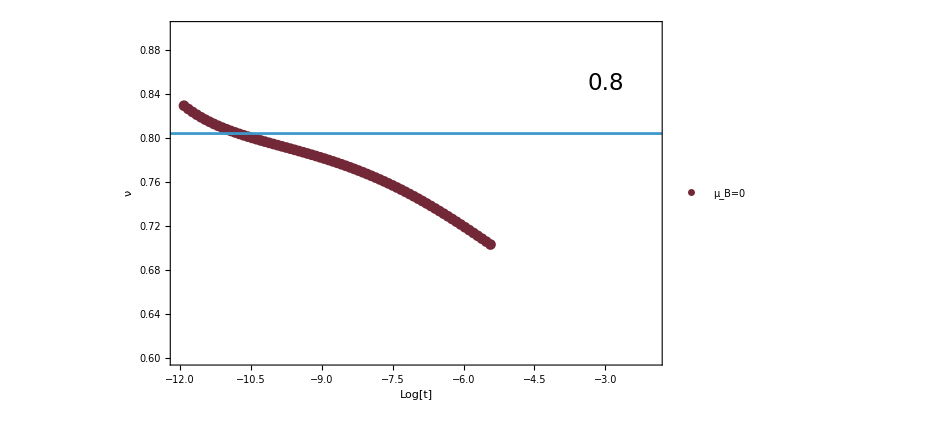

```mathematica
plotT=Show[ListPlot[{(*b1mub0,(*b1mub50,b1mub100,b1mub150,b1mub200,b1mub250,*)b1mub300(*,b1mub350*),b1mub400(*,b1mub450*),b1mub500,(*,b1mub550*)b1mub600,b1mub650,*)b1mub700(*,(*b1mub703,*)(*b1mub705,*)b1mub707,b1mub710,b1mub715,b1mub716p5*)},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.05}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0"(*,"μ_B=50 MeV","μ_B=100 MeV","μ_B=150 MeV","μ_B=200 MeV","μ_B=250 MeV"*),"μ_B=300 MeV"(*,"μ_B=350 MeV"*),"μ_B=400 MeV",(*"μ_B=450 MeV",*)"μ_B=500 MeV"(*,"μ_B=550 MeV"*),"μ_B=600 MeV","μ_B=650 MeV","μ_B=700 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{0.6,0.9}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.8043},{10,0.8043}}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.85}]}]
```

```mathematica
(*Export["./Tscaling.pdf",plotT]*)
```

```mathematica
Export["./LOdata/mub0.dat",b1mub0];
Export["./LOdata/mub300.dat",b1mub300];
Export["./LOdata/mub400.dat",b1mub400];
Export["./LOdata/mub500.dat",b1mub500];
Export["./LOdata/mub600.dat",b1mub600];
Export["./LOdata/mub650.dat",b1mub650];
Export["./LOdata/mub700.dat",b1mub700];
```

```mathematica
Log[0.01/700]
```

-11.1563